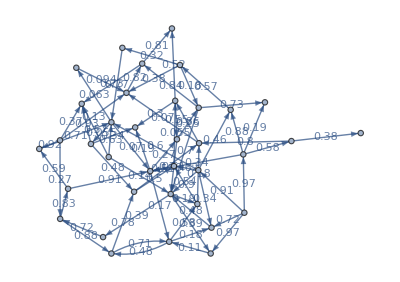

{1,26,4,22,11,21,36}

```mathematica
nVertex=36;
nEdges=2nVertex;
graph=RandomGraph[{nVertex,nEdges}, DirectedEdges->True, EdgeWeight->Table[RandomReal[{0,1}, WorkingPrecision->2], {i, nEdges}],EdgeLabels->"EdgeWeight"]
FindShortestPath[graph,1,nVertex]
```

```mathematica
EdgeW=AnnotationValue[graph,EdgeWeight]
EdgeL=EdgeList[graph]
```

{0.19,0.39,0.39,0.71,0.78,0.88,0.83,0.97,0.72,0.97,0.91,0.38,0.8,0.18,0.9,0.82,0.11,0.71,0.48,0.51,0.25,0.27,0.17,0.19,0.55,0.52,0.3,0.48,0.58,0.18,0.7,0.73,0.84,0.094,0.38,0.18,0.32,0.14,0.57,0.63,0.07,0.063,0.055,0.59,0.91,0.19,0.58,0.34,0.88,0.54,0.34,0.6,0.46,0.62,0.72,0.77,0.57,0.07,0.86,0.27,0.37,0.13,0.92,0.3,0.5,0.51,0.055,0.73,0.81,0.93,0.34,0.48}

{1->8,1->10,1->26,3->16,3->33,4->3,4->22,5->10,5->12,5->24,5->25,7->29,7->31,8->31,8->34,9->35,10->16,11->21,12->1,13->1,13->17,14->13,14->16,14->28,15->13,15->23,15->28,16->3,16->8,16->12,17->1,17->2,17->35,18->9,19->9,19->17,19->27,20->1,20->6,20->21,21->14,21->18,21->36,22->11,22->14,24->2,24->7,24->14,24->30,25->1,25->12,25->21,25->30,25->34,26->4,27->21,30->19,31->9,31->15,32->4,32->6,32->9,32->11,33->31,33->34,34->14,34->15,35->6,35->23,36->6,36->28,36->33}

```mathematica
export=Table[{EdgeL[[i]][[1]],EdgeL[[i]][[2]], EdgeW[[i]]}, {i,1,nEdges}];
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["problem.txt", export, "Table"]
```

problem.txt